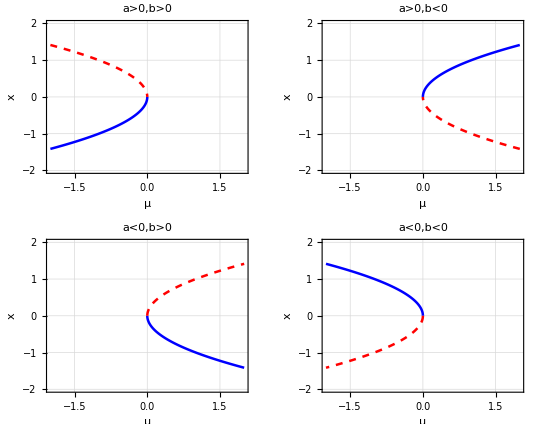

```mathematica
ClearAll[PlotBifurcation];

PlotBifurcation[f_,x_Symbol,mu_Symbol,muRange_List,xRange_List,label_]:=Module[{dfdx,stablePlot,unstablePlot},(*1. 计算导数*)dfdx=D[f,x];
(*2. 绘制稳定分支 (df/dx<0)*)stablePlot=ContourPlot[f==0,{mu,muRange[[1]],muRange[[2]]},{x,xRange[[1]],xRange[[2]]},ContourStyle->{Blue,Thickness[0.005]},(*使用替换确保计算正确*)RegionFunction->Function[{mVal,xVal,z},(dfdx/. {mu->mVal,x->xVal})<0],PlotPoints->50,MaxRecursion->3];
(*3. 绘制不稳定分支 (df/dx>0)*)unstablePlot=ContourPlot[f==0,{mu,muRange[[1]],muRange[[2]]},{x,xRange[[1]],xRange[[2]]},ContourStyle->{Red,Dashed,Thickness[0.005]},RegionFunction->Function[{mVal,xVal,z},(dfdx/. {mu->mVal,x->xVal})>0],PlotPoints->50,MaxRecursion->3];
(*4. 合并图形并修正 PlotRange 优先级*)Show[{stablePlot,unstablePlot},Axes->True,Frame->True,FrameLabel->{ToString[mu],ToString[x]},PlotLabel->label,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.5]],(*修正点：直接写出范围，mu 对应横轴，x 对应纵轴*)PlotRange->{muRange,xRange},ImageSize->Medium,AspectRatio->0.8]]
Clear[x,mu];
GraphicsGrid[{{PlotBifurcation[μ+x^2,x,μ,{-2,2},{-2,2},"a>0,b>0"],PlotBifurcation[μ-x^2,x,μ,{-2,2},{-2,2},"a>0,b<0"]},{PlotBifurcation[-μ+x^2,x,μ,{-2,2},{-2,2},"a<0,b>0"],PlotBifurcation[-μ-x^2,x,μ,{-2,2},{-2,2},"a<0,b<0"]}}]
```

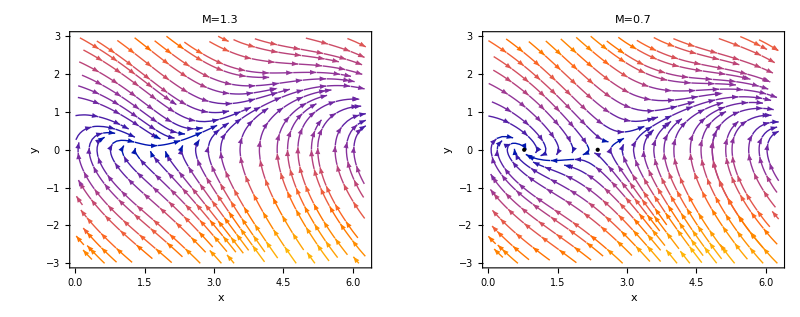

```mathematica
GraphicsRow[{StreamPlot[{y,-y-Sin[x]+1.1},{x,0,2π},{y,-3,3},AspectRatio->0.8,PlotLabel->"M=1.3",FrameLabel->{"x","y"}],StreamPlot[{y,-y-Sin[x]+0.7},{x,0,2π},{y,-3,3},Epilog->{PointSize[Medium],Point[{ ArcSin[0.7],0}],Point[{Pi- ArcSin[0.7],0}]},AspectRatio->0.8,PlotLabel->"M=0.7",FrameLabel->{"x","y"}]}]
```

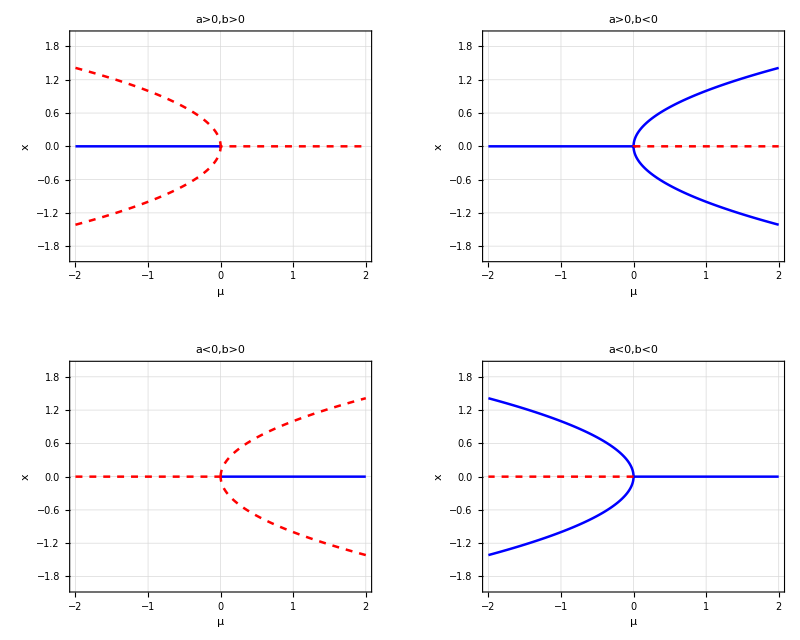

```mathematica
Clear[x,mu];
GraphicsGrid[{{PlotBifurcation[μ x+x^3,x,μ,{-2,2},{-2,2},"a>0,b>0"],PlotBifurcation[μ x-x^3,x,μ,{-2,2},{-2,2},"a>0,b<0"]},{PlotBifurcation[-μ x+x^3,x,μ,{-2,2},{-2,2},"a<0,b>0"],PlotBifurcation[-μ x-x^3,x,μ,{-2,2},{-2,2},"a<0,b<0"]}}]
```